```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
(* if rot is modified, conum should be modified in consequence *)
rot=0; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

idos(p,q)=pF_(n-1)+qF_n

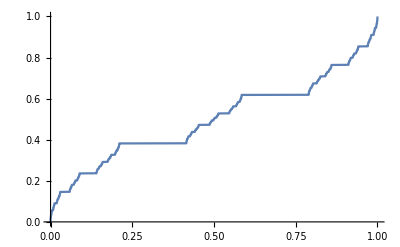

```mathematica
ρ=0.5;
n=17;
ham=hp[n-2,ρ,1.];
{val,vec}=Eigensystem[ham];
ord=Ordering[val];
vec=vec[[ord]];
val=val[[ord]];
(* translate and scale spectrum btw 0 and 1 *)
val=(val-val[[1]])/(val[[-1]]-val[[1]]);
idos=Table[{val[[i]],i/Fibonacci[n]},{i,Fibonacci[n]}];
(* p = -1, q = 1 *)
p1={val[[#]],#}&[Fibonacci[n-2]+1];
(* p = 1, q = 0*)
p2={val[[#]],#}&[Fibonacci[n-1]];
ListPlot[idos,Joined->True,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"idoslog.pdf",%]
```

/home/nicolas/git/talks/Fractals LPS june 2015/idoslog.pdf

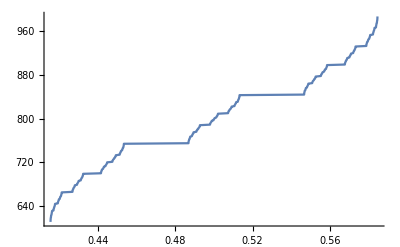

```mathematica
(* p = 4, q = -2 *)
lab1=4Fibonacci[n-1]-2Fibonacci[n]+1;
p1={val[[#]],#}&[lab1];
(* p = -4, q = 3 *)
lab2=-4Fibonacci[n-1]+3Fibonacci[n];
p2={val[[#]],#}&[lab2];
ListPlot[idos[[Fibonacci[n-2]+1;;Fibonacci[n-1]]],Joined->True,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"idos2.pdf",%]
```

/home/nicolas/git/talks/Fractals LPS june 2015/idos2.pdf

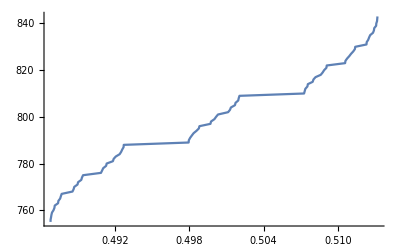

```mathematica
ListPlot[idos[[lab1;;lab2]],Joined->True,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"idos3.pdf",%]
```

/home/nicolas/git/talks/Fractals LPS june 2015/idos3.pdf